```mathematica
(* This does the stack of triangular Plaquettes --- reproducing David Berensteins notebook

The full form is not yet implemented 

H = \sum_s[g^2 E(s)^2_s + 1/g^2 B(s)^2 + alpha Link (B(s)_extra)^2 ]
 
All term sare positve: With Wilson Plaq
B^2(s) = Tr[1 - U_p - U^\dag_p](s) 
 (B(s)_etra)^2 = \sum_s Tr[2 - U(s)U^\dag(s+1) - U(s+1)U^\dag(s)] 

For U(1) Qubits Links:   U      --> sigma^+ = (sigma^x + i sigma^y)/2
                        U^\dag --> sigma^- = (sigma^x - i sigma^y)/2

E(s) = sigma^z(s) +  sigma^z(s+1)

Conventions for Qubit kernel construction *)

Sigma[0] = IdentityMatrix[2]
Sigma[1] = {{0, 1}, {1, 0}}
Sigma[2] = {{0, -I}, {I, 0}}
Sigma[3] = {{1, 0}, {0, -1}}
SigmaP= (Sigma[1]+ I*Sigma[2])/2
SigmaM= (Sigma[1]- I*Sigma[2])/2
```

{{1,0},{0,1}}

{{0,1},{1,0}}

{{0,-ⅈ},{ⅈ,0}}

{{1,0},{0,-1}}

{{0,1},{0,0}}

{{0,0},{1,0}}

```mathematica
F
```

F

```mathematica
(* Start one layer *)
(* Kronecker builds multi-Qubit tensor:  Left most matrix has fast  -- low bit -- convention 
Lables of N = nQubit tensor should be   sigma_{N} x sigma_{N-1} x  ... x  sigma_{0}   *)
(* Plaquette term *)
```

```mathematica
(* Insert FullSigma[ a = sigma_type , j = postion = 0,1,..., nQubit-1] *)
```

```mathematica
FullSigma[ a_, j_, nQubit_]:=KroneckerProduct[IdentityMatrix[2^(nQubit-j -1)], Sigma[a], IdentityMatrix[2^j]]
MatrixForm[FullSigma[3, 1, 2]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
(* Plaquetts  at s = layer number *)
```

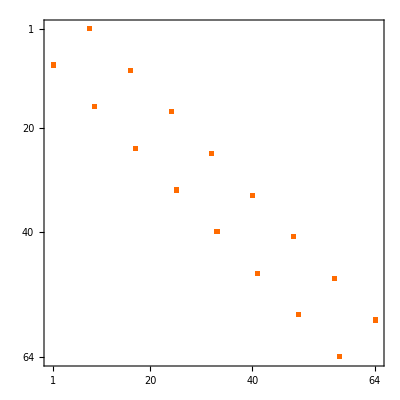

```mathematica
H3single[s_, nQubit_] := KroneckerProduct[ IdentityMatrix[2^(3*(s-1))],SigmaP, SigmaP, SigmaP,IdentityMatrix[2^(nQubit-3*s)]]+KroneckerProduct[IdentityMatrix[2^(3*(s-1))], SigmaM, SigmaM, SigmaM, IdentityMatrix[2^(nQubit-3*s)]]
MatrixPlot[H3single[2,6]]
```

```mathematica
H3s[nQubit_] := Sum[H3single[s, nQubit],{s,1,nQubit/3}]
```

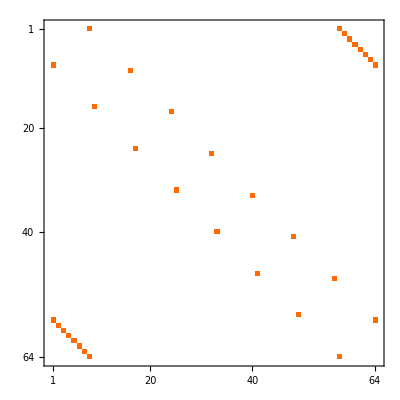

```mathematica
MatrixPlot[H3s[6]]
```

```mathematica
(* Electric term between layers for two layer of triangular plaquette sigmaz_{j+3) x sigmaz(j) note + convention on Qubit operators *)
 
H1s[nQubit_] := Sum[FullSigma[3,Mod[j+3,nQubit], nQubit].FullSigma[3, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]
```

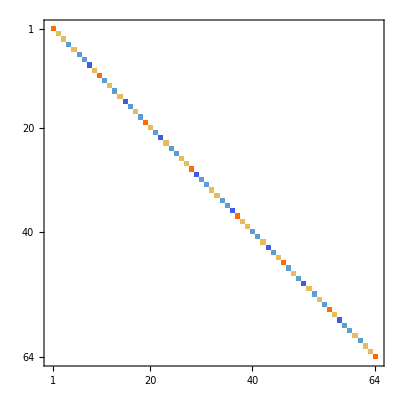

```mathematica
MatrixPlot[H1s[6]]
```

```mathematica
(* XX + YY chain *)
```

```mathematica
H2s[nQubit_] :=Sum[FullSigma[1,Mod[j+3,nQubit], nQubit].FullSigma[1, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]+
Sum[FullSigma[2,Mod[j+3,nQubit], nQubit].FullSigma[2, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]
```

```mathematica
(* Sign are choosen to be "right" of Hamilton *)
```

```mathematica
H[g_, alpha_, nQubit_]:=((g^2)/2)*H1s[nQubit]-  alpha*H2s[nQubit] - (1/(2*g^2))*H3s[nQubit]
```

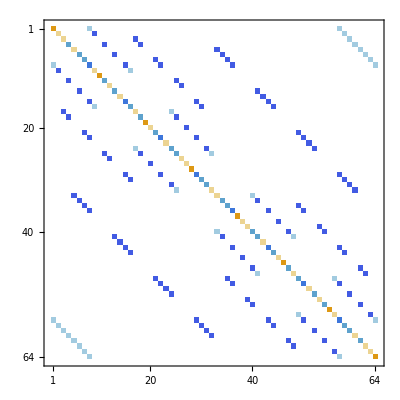

```mathematica
MatrixPlot[H[1, 1, 6]]
```

```mathematica
Eigs[g_, alpha_, nQubit_, k_] := Sort[Eigenvalues[H[g, alpha, nQubit], k], Less]
```

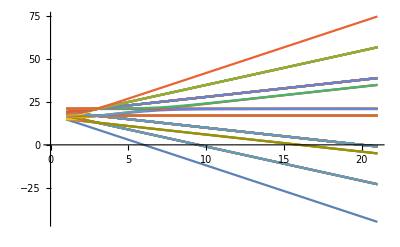

```mathematica
ListPlot[Transpose[Table[Eigs[1, c, 6, 2^6] +18, {c, 0, 5, 0.25}]], Joined->True]
```

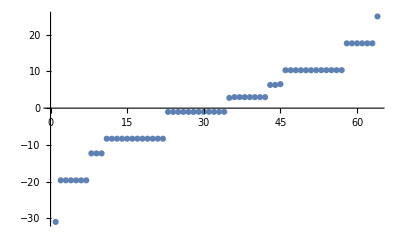

```mathematica
ListPlot[Eigs[1, 2.33,6 , 2^6]]
```

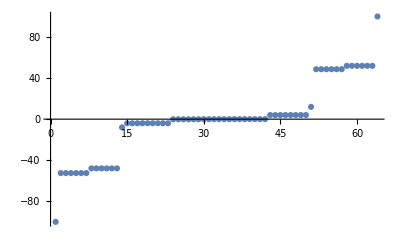

```mathematica
ListPlot[Eigs[0.1, 1,6 , 2^6]]
```

```mathematica
Eigs[1, 2.33,6 , 2^6]//N
```

{-30.9674,-19.651,-19.651,-19.651,-19.651,-19.651,-19.651,-12.32,-12.32,-12.32,-8.32,-8.32,-8.32,-8.32,-8.32,-8.32,-8.31378,-8.31378,-8.31378,-8.31378,-8.31378,-8.31378,-1.02204,-1.02204,-1.02204,-1.02204,-1.02204,-1.02204,-1.,-1.,-1.,-1.,-1.,-1.,2.79466,3.,3.,3.,3.,3.,3.,3.,6.32,6.32,6.5327,10.32,10.32,10.32,10.32,10.32,10.32,10.342,10.342,10.342,10.342,10.342,10.342,17.6448,17.6448,17.6448,17.6448,17.6448,17.6448,24.96}

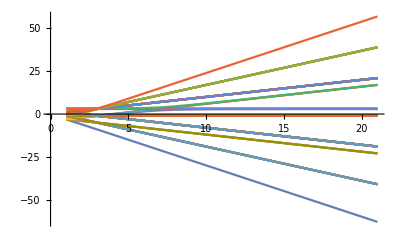

```mathematica
ListPlot[Transpose[Table[Eigs[1, c, 6, 2^6], {c, 0,5, 0.25}]], Joined->True]
```

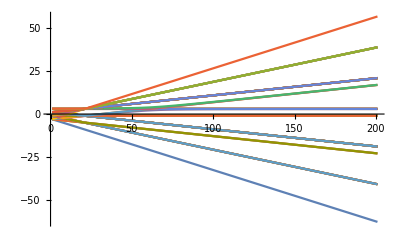

```mathematica
ListPlot[Transpose[Table[Eigs[1, b, 6, 2^6], {b, 0, 5, 0.025}]], Joined->True]
```